```mathematica
DeltaE=0.1;


dVec[kx_,ky_,dA1_,eps0_]:={DeltaE*Sin[kx]+dA1*(Cos[kx]+Cos[ky]),DeltaE*Sin[ky],-2*(Cos[kx]+Cos[ky])-eps0};


integrandFormula[kx_,ky_,dA1_,eps0_]=FullSimplify[With[{d=dVec[kx,ky,dA1,eps0]},Dot[d,Cross[D[d,kx],D[d,ky]]]/(Norm[d]^3)]];


computeChern[dA1_,eps0_]:=Module[{val},val=Quiet[(1/(4 Pi))*NIntegrate[integrandFormula[kx,ky,dA1,eps0],{kx,-Pi,Pi},{ky,-Pi,Pi},PrecisionGoal->5,AccuracyGoal->6,MaxRecursion->20,Method->"GlobalAdaptive"]];
Round[val]];

dA1Range=Range[0,1.5*DeltaE,0.005];
eps0Range=Range[0,4.1,0.01];


LaunchKernels[];


DistributeDefinitions[DeltaE,dVec,integrandFormula,computeChern];


phaseData=ParallelTable[{dA1/DeltaE,eps0,computeChern[dA1,eps0]},{dA1,dA1Range},{eps0,eps0Range},Method->"FinestGrained" ];

plotData=Flatten[phaseData,1];
```

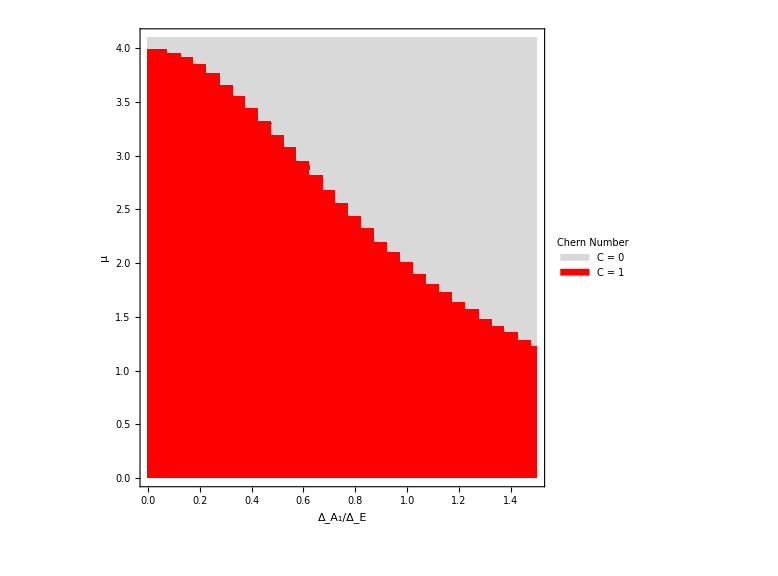

```mathematica
ListDensityPlot[plotData,ColorFunction->(Switch[Round[#],0,LightGray,1,Red,_,White]&),ColorFunctionScaling->False,InterpolationOrder->0,
Frame->True,
Axes->False,
RotateLabel->False,
FrameStyle->Directive[Black,Thick],FrameLabel->{Style[Row[{Subscript["Δ",Subscript["A","1"]],"/",Subscript["Δ","E"]}],24,FontFamily->"Times New Roman",Black],Style["μ",24,FontFamily->"Times New Roman",Black]},FrameTicks->Automatic,LabelStyle->Directive[Black,18,FontFamily->"Times New Roman"],
PlotLegends->Placed[SwatchLegend[{LightGray,Red},{"C = 0","C = 1"},LegendLabel->Style["Chern Number",20,
FontFamily->"Times New Roman",Black],LabelStyle->Directive[Black,18,FontFamily->"Times New Roman"]],Right],
ImageSize->Large]
```